```mathematica
t=Pi/4;
c[x_]:=Cos[x];
v[x_]:=1-Cos[x];
vc[x_]:=1+Cos[x];
s[x_]:=Sec[x];
xs[x_]:=Sec[x]-1;

N[#[t]]&/@{c,v,xs,s,vc}
```

{0.707107,0.292893,0.414214,1.41421,1.70711}

```mathematica
0.01875/3
```

0.00625

```mathematica
1875/300000
```

1/160

```mathematica
{RGBColor[1,0.65,0.65],Pink,Darker[Pink],RGBColor["#ff69b5"]}
```

{RGBColor[1, 0.65, 0.65],RGBColor[1, 0.5, 0.5],RGBColor[Rational[2, 3], 0.33333333333333337, 0.33333333333333337],RGBColor[1., 0.4117647058823529, 0.7098039215686275]}

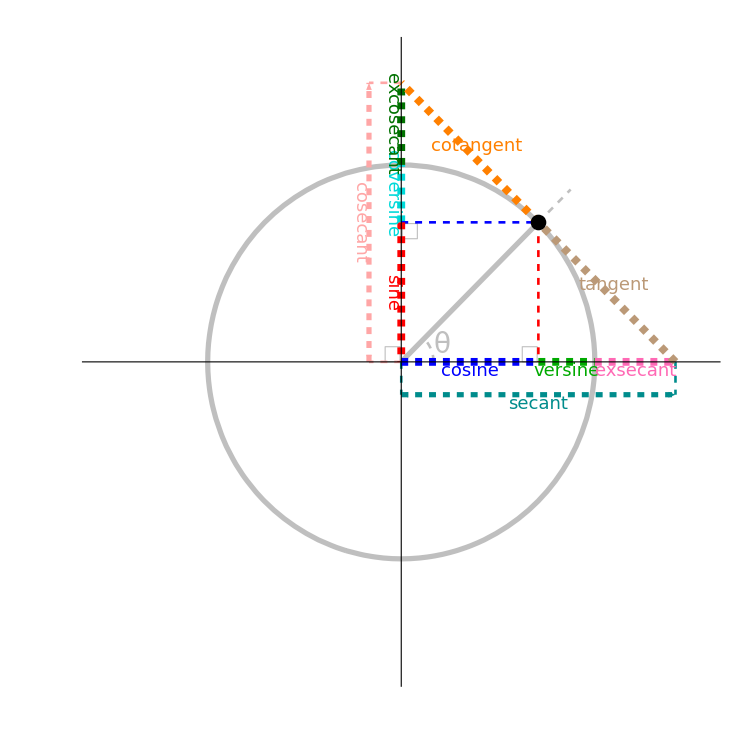

```mathematica
With[{r=3},
Module[{
xthick=Thickness[0.0075],
thick=Thickness[0.005],
thin=Thickness[0.0025],
dash=Dashed,
nodash=Dashing->None,
gray=GrayLevel[0.75],
ltpink=RGBColor[1,0.65,0.65],(* RGBColor["#ffc1cc"],*)
teal=RGBColor["#008c8c"],
dkgreen=Darker[Darker[Green]],
brpink=RGBColor["#ff69b5"],
green=Darker[Green],
tan=Lighter[Brown],
cyan=RGBColor[0,0.85,0.85],
orange=Orange,
red=Red,
blue=Blue,
black=Black,
n=(17/12)r,
r0=(1/6)r,
segexteps=(1/6)r,
sqeps=(1/13)r,
pinkeps=(1/6)r,
tealeps=(1/6)r,
eps0=(1/160)r,
texteps=(11/240)r,
xeps=(5/24)r,
yeps=(1/12)r,
st,cf,ef,ff
},

ClearAll[st];
st[s_String,fs_:18,sl_:Italic]:=Style[s,FontSize->fs,FontFamily->"Times",FontSlant->sl];
cf[s_]:=CapForm[s];
ef[s_]:=EdgeForm[s];
ff[s_]:=FaceForm[s];

ContourPlot[
x^2+y^2==r^2,
{x,-r-1,r+1},{y,-r-1,r+1},
Frame->None,
Axes->True,
Ticks->None,
ContourStyle->{thick,gray},

Epilog->
{
(* =========================== *)
(* Gray Ray Segment *)
cf["Square"],
nodash,
thick,
gray,
Line[{{0,0},{n/2,n/2}}],
(* Ray Segment Extension *)
dash,
thin,
gray,
Line[{{n/2,n/2},{n/2+segexteps,n/2+segexteps}}],
(* =========================== *)
(* Right Angle Squares *)
nodash,
thin,
ff[RGBColor[1,1,1,0]],
ef[gray],
Rectangle[{-sqeps-eps0,0},{-eps0,sqeps}] (* Bottom Left*),
Rectangle[{n/2-sqeps-eps0,0},{n/2-eps0,sqeps}] (* Bottom Right*),
Rectangle[{eps0,n/2-sqeps-eps0},{sqeps+eps0,n/2-eps0}] (* Top Left*),
(* =========================== *)
(* Angle Circle *)
nodash,
thin,
gray,
Circle[{0,0},r0,{0,Pi/4}],
(* =========================== *)
(* Light Pink Dashed Lines *)
dash,
thin,
ltpink,
Line[{{0,n},{-pinkeps,n}}],
Line[{{0,0},{-pinkeps,0}}],
(* Light Pink Arrow *)
nodash,
thick,
ltpink,
Arrowheads[{-.05,.05}],
Arrow[Line[{{-pinkeps,0},{-pinkeps,n}}]],
(* Teal Dashed Lines *)
dash,
thin,
teal,
Line[{{n,0},{n,-tealeps}}],
Line[{{0,0},{0,-tealeps}}],
(* Teal Arrow *)
nodash,
thick,
teal,
Arrowheads[{-.05,.05}],
Arrow[Line[{{0,-tealeps},{n,-tealeps}}]],
(* =========================== *)
(* Cyan Segment *)
xthick,
nodash,
cyan ,
Line[{{0,n/2},{0,r}}],
(* Dark Green Segment *)
xthick,
nodash,
dkgreen,
Line[{{0,r},{0,n}}],
(* Green Segment *)
xthick,
nodash,
green ,
Line[{{n/2,0},{r,0}}],
(* Bright Pink Segment *)
xthick,
nodash,
brpink ,
Line[{{r,0},{n,0}}],
(* Secondary Red Segment *)
thin,
dash,
red ,
Line[{{n/2,n/2},{n/2,0}}],
(* Secondary Blue Segment *)
thin,
dash,
blue,
Line[{{0,n/2},{n/2,n/2}}],
(* Main Red Segment *)
xthick,
nodash,
red,
Line[{{0,n/2},{0,0}}],
(* Main Blue Segment *)
xthick,
nodash,
blue,
Line[{{0,0},{n/2,0}}],
(* Tan Segment *)
cf["Round"],
xthick,
nodash,
tan,
Line[{{n,0},{n/2,n/2}}],
(* Orange Segment *)
xthick,
nodash,
orange,
Line[{{n/2,n/2},{0,n}}],
(* =========================== *)
(* Black Point *)
cf["Round"],
black,
PointSize[0.015],
Point[{{n/2,n/2}}],
(* =========================== *)
(* Gray θ Text *)
gray,
Text[st["θ",28,Plain],{xeps,yeps}],
(* Blue Text *)
blue,
Text[st["cosine"],{(n/2)/2,-texteps}],
(* Green Text *)
green,
Text[st["versine"],{(r+n/2)/2,-texteps}],
(* Bright Pink Text *)
brpink,
Text[st["exsecant"],{(r+n)/2,-texteps}],
(* Teal Text *)
teal,
Text[st["secant"],{n/2,-tealeps-texteps}],
(* Red Text *)
red,
Text[st["sine"],{-texteps,(n/2)/2},Automatic,{0,-1}],
(* Cyan Text *)
cyan,
Text[st["coversine"],{-texteps,(r+(n/2))/2},Automatic,{0,-1},Background->RGBColor[1,1,1,0.875]],
(* Dark Green Text *)
dkgreen,
Text[st["excosecant"],{-texteps,(r+n)/2},Automatic,{0,-1}],,
(* Light Pink Text *)
ltpink,
Text[st["cosecant"],{-pinkeps-texteps,n/2},Automatic,{0,-1}],
(* Orange Text *)
orange,
Text[st["cotangent"],{(n/2)/2+(3/4)texteps,(n+(n/2))/2+(3/4)texteps},Automatic,{1,-1}],
(* Tan Text *)
tan,
Text[st["tangent"],{(n+(n/2))/2+(3/4)texteps,(n/2)/2+(3/4)texteps},Automatic,{1,-1}],
(*(* Bottom Box *)
ff[RGBColor[1,1,1,0.75]],
ef[{gray,dash}],
Rectangle[{n/8,-n+0.8},{n-n/8,-n/4}] (* {-3n/4,-3n/4}*),
(* Top Box *)
ff[RGBColor[1,1,1,0.75]],
ef[{gray,dash}],
Rectangle[{n/8-(5/4)n+n/8,-n+0.8+n},{n-n/8-n-n/8,-n/4+n}] (* {-3n/4,-3n/4}*)*)
},
ImageSize->750,
PlotRange->{{-(19/12)r,(19/12)r},{-(19/12)r,(19/12)r}}(* {{-(7/6)r,(19/12)r},{-(33/24)r,(19/12)r}} *)]]]
```

```mathematica
{GrayLevel[0.75],LightGray}
```

{GrayLevel[0.75],GrayLevel[0.85]}

```mathematica
56*55
```

3080

```mathematica
52*51
```

2652

```mathematica
123*456
```

56088

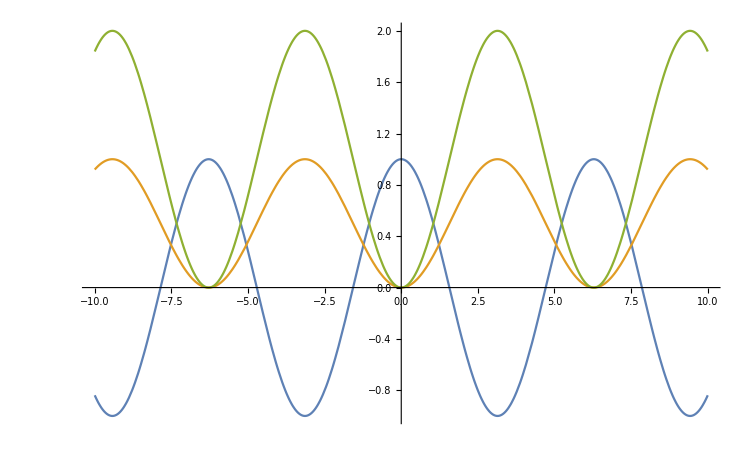

```mathematica
Plot[{Cos[x],Haversine[x],Versine[x]},{x,-10,10},ImageSize->750]
```

```mathematica
1111*11
```

12221

```mathematica
1234*11
```

13574

```mathematica
158*11
```

1738

```mathematica
Cyan
```

RGBColor[0, 1, 1]

```mathematica
{RGBColor[0,0.9,0.9],Darker@Cyan,RGBColor["#008c8c"]}
```

{RGBColor[0, 0.9, 0.9],RGBColor[0, Rational[2, 3], Rational[2, 3]],RGBColor[0., 0.5490196078431373, 0.5490196078431373]}

```mathematica
({n/8,-n}-{n-n/8,-n/4})
```

{-(3 n)/4,-(3 n)/4}

```mathematica
n
```

17/4

```mathematica
ClearAll[n]
```

```mathematica
Options[Graphics[{Text[st["coversine"],{-1,(3+(5/2))/2},Automatic,{0,-1},Background->RGBColor[1,1,1,0.875]]}]]
```

{}

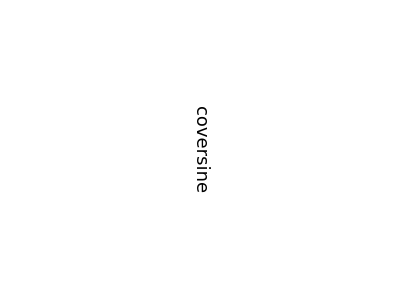
```mathematica
-Graphics-//Options
```

{}

```mathematica
FullForm[-Graphics-]
```

Graphics[Inset[Style["coversine",Rule[FontFamily,"Times"],Rule[FontSize,18],Rule[FontSlant,Italic]],List[-1,Rational[11,4]],Automatic,Automatic,List[0,-1],Rule[Background,RGBColor[1,1,1,0.875]]]]

```mathematica
-Graphics-//Options
```

{AspectRatio→1/GoldenRatio,Axes→{True,True},AxesLabel→{None,None},AxesOrigin→{0,0},DisplayFunction→Identity,Frame→{{False,False},{False,False}},FrameLabel→{{None,None},{None,None}},FrameTicks→{{Automatic,Automatic},{Automatic,Automatic}},GridLines→{None,None},GridLinesStyle→Directive[GrayLevel[0.5, 0.4]],ImagePadding→All,ImageSize→750,Method→{DefaultBoundaryStyle→Automatic,DefaultGraphicsInteraction→{Version→1.2,TrackMousePosition→{True,False},Effects→{Highlight→{ratio→2},HighlightPoint→{ratio→2},Droplines→{freeformCursorMode→True,placement→{x→All,y→None}}}},DefaultMeshStyle→AbsolutePointSize[6],ScalingFunctions→None,CoordinatesToolOptions→{DisplayFunction→({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),CopiedValueFunction→({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}},PlotRange→{{-10,10},{-1.,2.}},PlotRangeClipping→True,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}},Ticks→{Automatic,Automatic}}